# Inspect results

### Load data

```mathematica
toPs = 5.31915
```

5.31915

No closure

```mathematica
(**)
Clear[rawdataChi20,headersChi20,dataChi20,nnChi20];
rawdataChi20 = Import[NotebookDirectory[]<>"Sample_evol/measurements_Chi20.dat","Table"];
headersChi20 = Drop[rawdataChi20[[1]],1];
dataChi20 = Drop[rawdataChi20,1];
nnChi20=Length[dataChi20[[All,11]]]
```

500

```mathematica
Clear[rawdataChi8,headersChi8,dataChi8,nnChi8];
rawdataChi8 = Import[NotebookDirectory[]<>"Sample_evol/measurements_Chi8.dat","Table"];
headersChi8 = Drop[rawdataChi8[[1]],1];
dataChi8 = Drop[rawdataChi8,1];
nnChi8=Length[dataChi8[[All,11]]]
```

500

Data Alex

```mathematica
Clear[dataAlex];
dataAlex=Import[NotebookDirectory[]<>"Sample_evol/meas_alex_sys.csv","Table","FieldSeparators"->{";"}];
Clear[dataAlexN10];
dataAlexN10=Import[NotebookDirectory[]<>"Sample_evol/meas_alex_N10.csv","Table","FieldSeparators"->{";"}];
```

No Closure

```mathematica
(*TDVP1 Data M=20 N=6*)
rawdataTDVP1 = Import[NotebookDirectory[]<>"TDVP1_Tama/critico.dat","Table"];
headersTDVP1 = Drop[rawdataTDVP1[[1]],1];
dataTDVP1 = Drop[rawdataTDVP1,1];
nnTDVP1=Length[rawdataTDVP1[[All]]]
```

501

Data Markovian Closure

```mathematica
(*MC Data M=20 N=6*)
rawdataMC = Import[NotebookDirectory[]<>"Sample_evol/measurements_MC_N6_Chi20_2.dat","Table"];
headersMC = Drop[rawdataMC[[1]],1];
dataMC = Drop[rawdataMC,1];
nnMC=Length[dataMC[[All]]]
```

500

Markovian Closure QTech

```mathematica
(*TDVP1-qTech Data M=20 N=6*)
rawdataTDVP1Q = Import[NotebookDirectory[]<>"Res_TDVP1_noPermute/measurements.dat","Table"];
headersTDVP1Q = Drop[rawdataTDVP1Q[[1]],1];
dataTDVP1Q = Drop[rawdataTDVP1Q,1];
nnTDVP1Q=Length[rawdataTDVP1Q[[All]]]
```

501

Markovian Closure: Permutation (1,2)(3,4)(5,6)

```mathematica
rawdataTDVP1QP1 = Import[NotebookDirectory[]<>"Res_TDVP1_Permute1/measurements.dat","Table"];
headersTDVP1QP1 = Drop[rawdataTDVP1QP1[[1]],1];
dataTDVP1QP1 = Drop[rawdataTDVP1QP1,1];
nnTDVP1QP1=Length[rawdataTDVP1QP1[[All]]]
```

501

```mathematica
dataTDVP1Q[[All,1]]
```

{0.001,0.002,0.003,0.004,0.005,0.006,0.007,0.008,0.009,0.01,0.011,0.012,0.013,0.014,0.015,0.016,0.017,0.018,0.019,0.02,0.021,0.022,0.023,0.024,0.025,0.026,0.027,0.028,0.029,0.03,0.031,0.032,0.033,0.034,0.035,0.036,0.037,0.038,0.039,0.04,0.041,0.042,0.043,0.044,0.045,0.046,0.047,0.048,0.049,0.05,0.051,0.052,0.053,0.054,0.055,0.056,0.057,0.058,0.059,0.06,0.061,0.062,0.063,0.064,0.065,0.066,0.067,0.068,0.069,0.07,0.071,0.072,0.073,0.074,0.075,0.076,0.077,0.078,0.079,0.08,0.081,0.082,0.083,0.084,0.085,0.086,0.087,0.088,0.089,0.09,0.091,0.092,0.093,0.094,0.095,0.096,0.097,0.098,0.099,0.1,0.101,0.102,0.103,0.104,0.105,0.106,0.107,0.108,0.109,0.11,0.111,0.112,0.113,0.114,0.115,0.116,0.117,0.118,0.119,0.12,0.121,0.122,0.123,0.124,0.125,0.126,0.127,0.128,0.129,0.13,0.131,0.132,0.133,0.134,0.135,0.136,0.137,0.138,0.139,0.14,0.141,0.142,0.143,0.144,0.145,0.146,0.147,0.148,0.149,0.15,0.151,0.152,0.153,0.154,0.155,0.156,0.157,0.158,0.159,0.16,0.161,0.162,0.163,0.164,0.165,0.166,0.167,0.168,0.169,0.17,0.171,0.172,0.173,0.174,0.175,0.176,0.177,0.178,0.179,0.18,0.181,0.182,0.183,0.184,0.185,0.186,0.187,0.188,0.189,0.19,0.191,0.192,0.193,0.194,0.195,0.196,0.197,0.198,0.199,0.2,0.201,0.202,0.203,0.204,0.205,0.206,0.207,0.208,0.209,0.21,0.211,0.212,0.213,0.214,0.215,0.216,0.217,0.218,0.219,0.22,0.221,0.222,0.223,0.224,0.225,0.226,0.227,0.228,0.229,0.23,0.231,0.232,0.233,0.234,0.235,0.236,0.237,0.238,0.239,0.24,0.241,0.242,0.243,0.244,0.245,0.246,0.247,0.248,0.249,0.25,0.251,0.252,0.253,0.254,0.255,0.256,0.257,0.258,0.259,0.26,0.261,0.262,0.263,0.264,0.265,0.266,0.267,0.268,0.269,0.27,0.271,0.272,0.273,0.274,0.275,0.276,0.277,0.278,0.279,0.28,0.281,0.282,0.283,0.284,0.285,0.286,0.287,0.288,0.289,0.29,0.291,0.292,0.293,0.294,0.295,0.296,0.297,0.298,0.299,0.3,0.301,0.302,0.303,0.304,0.305,0.306,0.307,0.308,0.309,0.31,0.311,0.312,0.313,0.314,0.315,0.316,0.317,0.318,0.319,0.32,0.321,0.322,0.323,0.324,0.325,0.326,0.327,0.328,0.329,0.33,0.331,0.332,0.333,0.334,0.335,0.336,0.337,0.338,0.339,0.34,0.341,0.342,0.343,0.344,0.345,0.346,0.347,0.348,0.349,0.35,0.351,0.352,0.353,0.354,0.355,0.356,0.357,0.358,0.359,0.36,0.361,0.362,0.363,0.364,0.365,0.366,0.367,0.368,0.369,0.37,0.371,0.372,0.373,0.374,0.375,0.376,0.377,0.378,0.379,0.38,0.381,0.382,0.383,0.384,0.385,0.386,0.387,0.388,0.389,0.39,0.391,0.392,0.393,0.394,0.395,0.396,0.397,0.398,0.399,0.4,0.401,0.402,0.403,0.404,0.405,0.406,0.407,0.408,0.409,0.41,0.411,0.412,0.413,0.414,0.415,0.416,0.417,0.418,0.419,0.42,0.421,0.422,0.423,0.424,0.425,0.426,0.427,0.428,0.429,0.43,0.431,0.432,0.433,0.434,0.435,0.436,0.437,0.438,0.439,0.44,0.441,0.442,0.443,0.444,0.445,0.446,0.447,0.448,0.449,0.45,0.451,0.452,0.453,0.454,0.455,0.456,0.457,0.458,0.459,0.46,0.461,0.462,0.463,0.464,0.465,0.466,0.467,0.468,0.469,0.47,0.471,0.472,0.473,0.474,0.475,0.476,0.477,0.478,0.479,0.48,0.481,0.482,0.483,0.484,0.485,0.486,0.487,0.488,0.489,0.49,0.491,0.492,0.493,0.494,0.495,0.496,0.497,0.498,0.499,0.5}

```mathematica
headersMC
```

{time,N_11,N_21,N_31,N_41,N_51,N_61,N_71,N_81,N_82,N_83,N_84,N_85,N_86,N_87,Sx_1,Sz_1,re_over,im_over,Norm}

```mathematica
headersTDVP1
```

{time,N_11,N_21,N_31,N_41,N_51,N_61,N_71,N_81,N_82,N_83,N_84,N_85,N_86,N_87,Sx_1,Sz_1,re_over,im_over,Norm}

```mathematica
Position[headersMC,"re_over"][[1,1]]
Position[headersTDVP1,"re_over"]
```

18

{{18}}

```mathematica
dataMC
```

{{0.001,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.1577×10^-11,1.×10^-15,7.245×10^-12,1.×10^-15,5.58×10^-13,5.×10^-15,0.493549,0.994396,-0.0685884,1.},498,{0.5,4.00153×10^-7,1.80313×10^-6,4.8572×10^-6,0.000019708,0.000126923,0.000306078,0.00053267,0.000914474,0.00104669,0.00147626,0.000071894,0.000147202,0.00072215,0.000633843,5.36071×10^-9,-0.00777133,-0.000764536,0.000142259,0.133525}}
 |  |  |  |

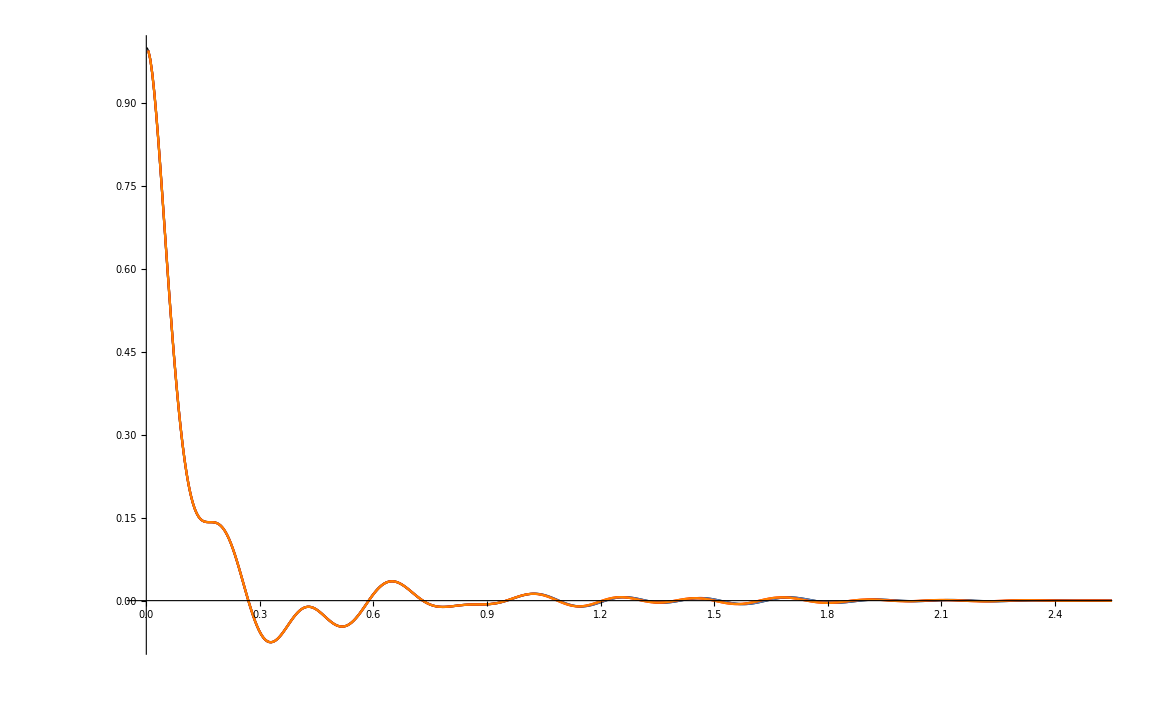

```mathematica
Show[
ListPlot[Transpose[{dataAlex[[All,1]]/0.188365,dataAlex[[All,2]]}],PlotRange->{{0,2.5},All},Joined->True,PlotStyle->{Black,Thick}],
ListPlot[Transpose[{toPs*Take[dataMC[[All,1]],All],Take[dataMC[[All,Position[headersMC,"re_over"][[1,1]]]],All]}],PlotRange->All,Joined->True,PlotStyle->Black],
ListPlot[Transpose[{toPs*dataTDVP1[[All,1]],dataTDVP1[[All,Position[headersTDVP1,"re_over"][[1,1]]]]}],Joined->True,PlotRange->All],
ListPlot[Transpose[{toPs*dataTDVP1Q[[All,1]],dataTDVP1Q[[All,Position[headersTDVP1Q,"re_over"][[1,1]]]]}],Joined->True,PlotStyle->Red,PlotRange->All],
ListPlot[Transpose[{toPs*dataTDVP1QP1[[All,1]],dataTDVP1QP1[[All,Position[headersTDVP1QP1,"re_over"][[1,1]]]]}],Joined->True,PlotStyle->Orange,PlotRange->All]
]
```

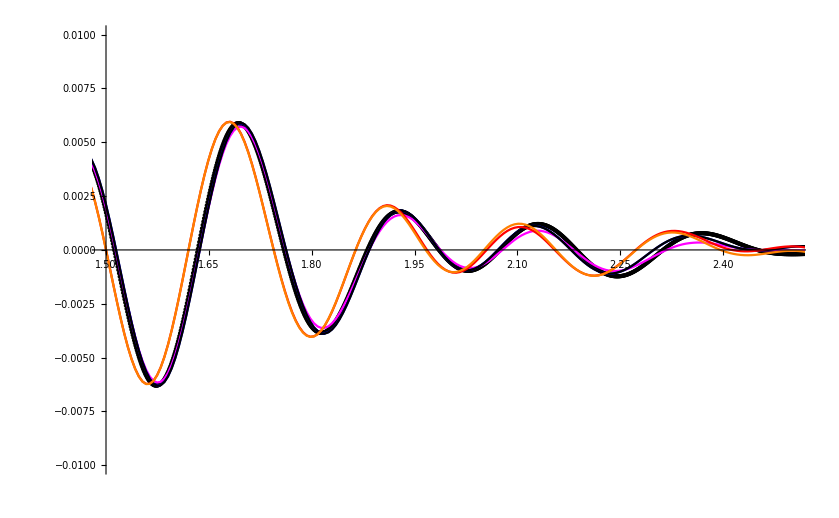

```mathematica
Show[
ListPlot[Transpose[{dataAlex[[All,1]]/0.188365,dataAlex[[All,2]]}],PlotRange->{{0,2.5},All},(*Joined->True,*)PlotStyle->{Black,Thick}],
ListPlot[Transpose[{dataChi20[[All,1]]*toPs,dataChi20[[All,12]]}],Joined->True,PlotRange->{{0,2.5},All},PlotStyle->Magenta],
ListPlot[Transpose[{toPs*dataTDVP1[[All,1]],dataTDVP1[[All,Position[headersTDVP1,"re_over"][[1,1]]]]}],Joined->True,PlotRange->All,PlotStyle->Blue],
ListPlot[Transpose[{toPs*Take[dataMC[[All,1]],All],Take[dataMC[[All,Position[headersMC,"re_over"][[1,1]]]],All]}],PlotRange->All,Joined->True,PlotStyle->Black],

ListPlot[Transpose[{toPs*dataTDVP1Q[[All,1]],dataTDVP1Q[[All,Position[headersTDVP1Q,"re_over"][[1,1]]]]}],Joined->True,PlotStyle->Red,PlotRange->All],
ListPlot[Transpose[{toPs*dataTDVP1QP1[[All,1]],dataTDVP1QP1[[All,Position[headersTDVP1QP1,"re_over"][[1,1]]]]}],Joined->True,PlotStyle->Orange,PlotRange->All],
PlotRange->{{1.5,2.5},{-0.01,0.01}},
AxesOrigin->{1.5,0}
]
```

```mathematica
dataMC[[All,1]]*toPs;
```

## Population chain site 10

```mathematica
headersMC
```

{time,N_11,N_21,N_31,N_41,N_51,N_61,N_71,N_81,N_82,N_83,N_84,N_85,N_86,N_87,Sx_1,Sz_1,re_over,im_over,Norm}

```mathematica
headersChi20
```

{time,N_11,N_21,N_31,N_41,N_51,N_61,N_71,N_81,Sx_1,Sz_1,re_over,im_over}

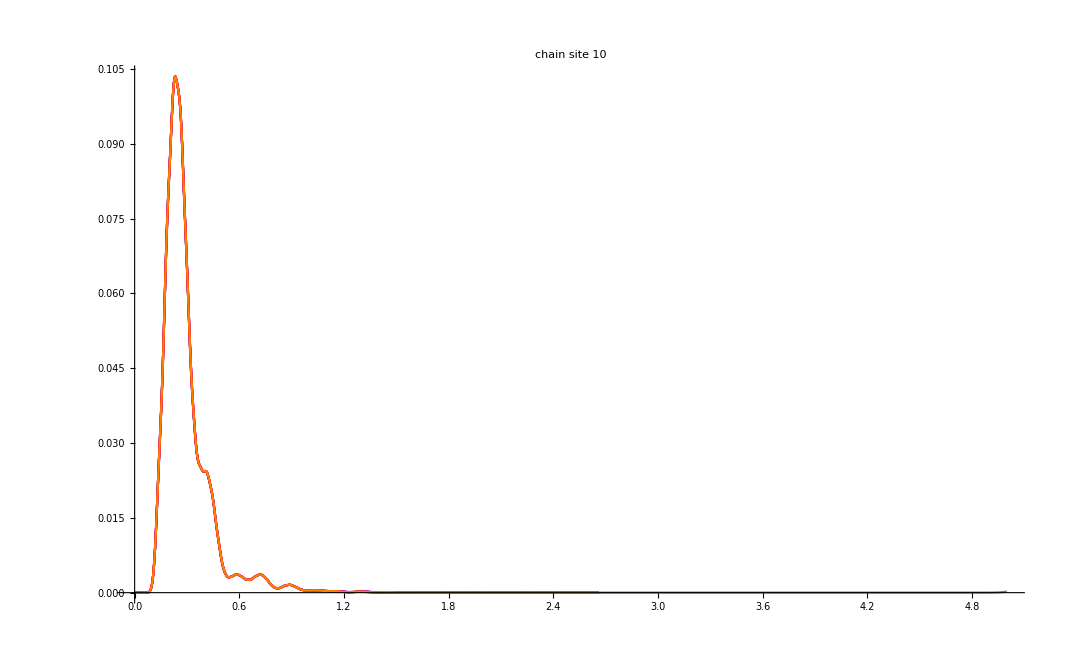

```mathematica
Show[
ListPlot[Transpose[{dataAlex[[All,1]]/0.188365,dataAlexN10[[All,2]]}],PlotRange->{{0,2.5},All},Joined->True],
ListPlot[Transpose[{dataChi20[[All,1]]*toPs,dataChi20[[All,2]]}],Joined->True,PlotRange->{{0,2.5},All},PlotStyle->Red],
ListPlot[Transpose[{dataMC[[All,1]]*toPs,dataMC[[All,2]]}],Joined->True,PlotRange->{{0,2.5},All},PlotStyle->Blue],
ListPlot[Transpose[{dataTDVP1[[All,1]]*toPs,dataTDVP1[[All,Position[headersTDVP1,"N_11"][[1,1]]]]}],Joined->True,PlotRange->{{0,2.5},All},PlotStyle->Magenta],
ListPlot[Transpose[{toPs*dataTDVP1Q[[All,1]],dataTDVP1Q[[All,Position[headersTDVP1Q,"N_11"][[1,1]]]]}],Joined->True,PlotStyle->Red,PlotRange->All],
ListPlot[Transpose[{toPs*dataTDVP1QP1[[All,1]],dataTDVP1QP1[[All,Position[headersTDVP1QP1,"N_11"][[1,1]]]]}],Joined->True,PlotStyle->Orange,PlotRange->All],
PlotRange->All,

PlotLabel->"chain site 10"
]
```

### Population chain site 20

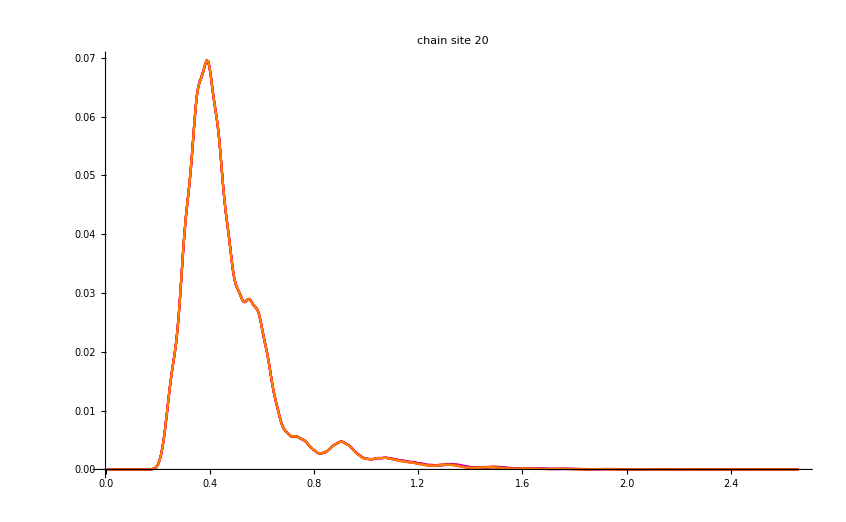

```mathematica
Show[
(*ListPlot[Transpose[{dataAlex[[All,1]]/0.188365,dataAlexN10[[All,2]]}],PlotRange->{{0,2.5},All},Joined->True],*)
ListPlot[Transpose[{dataChi20[[All,1]]*toPs,dataChi20[[All,3]]}],Joined->True,PlotRange->{{0,2.5},All},PlotStyle->Red],
ListPlot[Transpose[{dataMC[[All,1]]*toPs,dataMC[[All,3]]}],Joined->True,PlotRange->{{0,2.5},All},PlotStyle->Blue],
ListPlot[Transpose[{dataTDVP1[[All,1]]*toPs,dataTDVP1[[All,Position[headersTDVP1,"N_21"][[1,1]]]]}],Joined->True,PlotRange->{{0,2.5},All},PlotStyle->Magenta],
ListPlot[Transpose[{toPs*dataTDVP1Q[[All,1]],dataTDVP1Q[[All,Position[headersTDVP1Q,"N_21"][[1,1]]]]}],Joined->True,PlotStyle->Red,PlotRange->All],
ListPlot[Transpose[{toPs*dataTDVP1QP1[[All,1]],dataTDVP1QP1[[All,Position[headersTDVP1QP1,"N_21"][[1,1]]]]}],Joined->True,PlotStyle->Orange,PlotRange->All],
PlotRange->All,
PlotLabel->"chain site 20"
]
```

### Population chain site 30

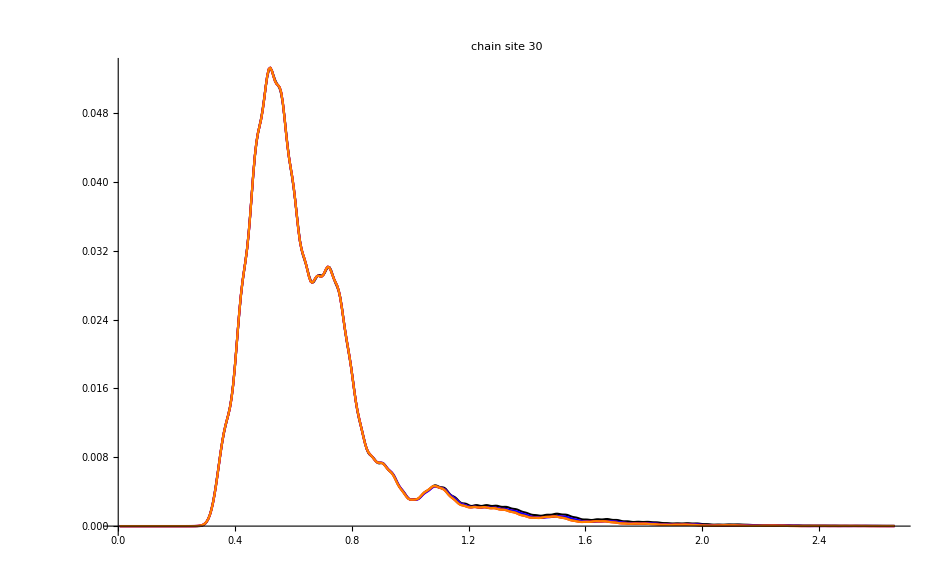

```mathematica
Show[
(*ListPlot[Transpose[{dataAlex[[All,1]]/0.188365,dataAlexN10[[All,2]]}],PlotRange->{{0,2.5},All},Joined->True],*)
ListPlot[Transpose[{dataChi20[[All,1]]*toPs,dataChi20[[All,4]]}],Joined->True,PlotRange->{{0,2.5},All},PlotStyle->Black],
ListPlot[Transpose[{dataTDVP1[[All,1]]*toPs,dataTDVP1[[All,Position[headersTDVP1,"N_31"][[1,1]]]]}],Joined->True,PlotRange->{{0,2.5},All},PlotStyle->Magenta],

ListPlot[Transpose[{dataMC[[All,1]]*toPs,dataMC[[All,4]]}],Joined->True,PlotRange->{{0,2.5},All},PlotStyle->Blue],
ListPlot[Transpose[{toPs*dataTDVP1Q[[All,1]],dataTDVP1Q[[All,Position[headersTDVP1Q,"N_31"][[1,1]]]]}],Joined->True,PlotStyle->Red,PlotRange->All],
ListPlot[Transpose[{toPs*dataTDVP1QP1[[All,1]],dataTDVP1QP1[[All,Position[headersTDVP1QP1,"N_31"][[1,1]]]]}],Joined->True,PlotStyle->Orange,PlotRange->All],
PlotRange->All,
PlotLabel->"chain site 30"
]
```

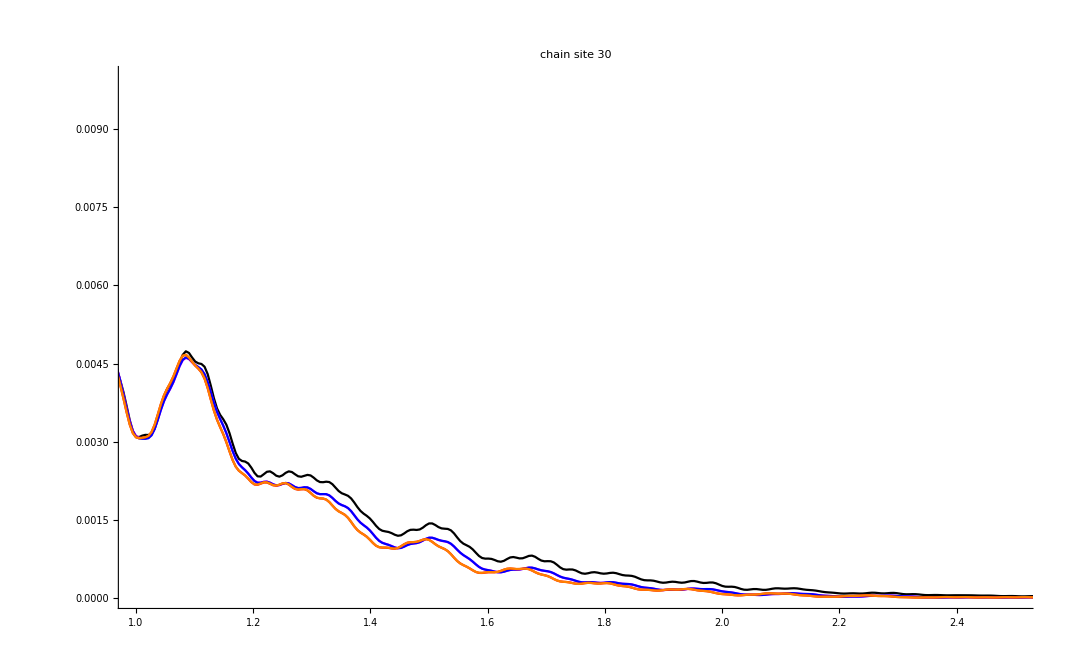

```mathematica
Show[
(*ListPlot[Transpose[{dataAlex[[All,1]]/0.188365,dataAlexN10[[All,2]]}],PlotRange->{{0,2.5},All},Joined->True],*)
ListPlot[Transpose[{dataChi20[[All,1]]*toPs,dataChi20[[All,4]]}],Joined->True,PlotRange->{{0,2.5},All},PlotStyle->Black],
ListPlot[Transpose[{dataTDVP1[[All,1]]*toPs,dataTDVP1[[All,Position[headersTDVP1,"N_31"][[1,1]]]]}],Joined->True,PlotRange->{{0,2.5},All},PlotStyle->Magenta],

ListPlot[Transpose[{dataMC[[All,1]]*toPs,dataMC[[All,4]]}],Joined->True,PlotRange->{{0,2.5},All},PlotStyle->Blue],
ListPlot[Transpose[{toPs*dataTDVP1Q[[All,1]],dataTDVP1Q[[All,Position[headersTDVP1Q,"N_31"][[1,1]]]]}],Joined->True,PlotStyle->Red,PlotRange->All],
ListPlot[Transpose[{toPs*dataTDVP1QP1[[All,1]],dataTDVP1QP1[[All,Position[headersTDVP1QP1,"N_31"][[1,1]]]]}],Joined->True,PlotStyle->Orange,PlotRange->All],
PlotLabel->"chain site 30",
PlotRange->{{1,2.5},{0,0.01}}
]
```

### Population chain site 40

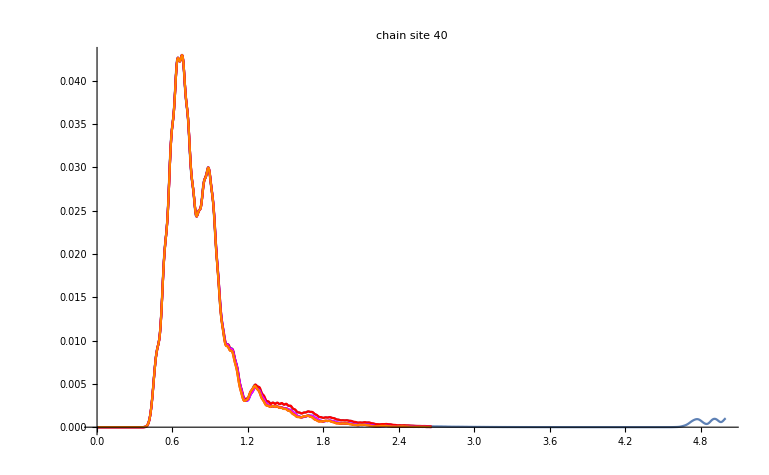

```mathematica
Show[
ListPlot[Transpose[{dataAlex[[All,1]]/0.188365,dataAlexN10[[All,3]]}],PlotRange->{{0,2.5},All},Joined->True],
ListPlot[Transpose[{dataChi20[[All,1]]*toPs,dataChi20[[All,5]]}],Joined->True,PlotRange->{{0,2.5},All},PlotStyle->Red],
ListPlot[Transpose[{dataMC[[All,1]]*toPs,dataMC[[All,5]]}],Joined->True,PlotRange->{{0,2.5},All},PlotStyle->Blue],
ListPlot[Transpose[{dataTDVP1[[All,1]]*toPs,dataTDVP1[[All,Position[headersTDVP1,"N_41"][[1,1]]]]}],Joined->True,PlotRange->{{0,2.5},All},PlotStyle->Magenta],
ListPlot[Transpose[{toPs*dataTDVP1Q[[All,1]],dataTDVP1Q[[All,Position[headersTDVP1Q,"N_41"][[1,1]]]]}],Joined->True,PlotStyle->Red,PlotRange->All],
ListPlot[Transpose[{toPs*dataTDVP1QP1[[All,1]],dataTDVP1QP1[[All,Position[headersTDVP1QP1,"N_41"][[1,1]]]]}],Joined->True,PlotStyle->Orange,PlotRange->All],
PlotRange->All,
PlotLabel->"chain site 40"
]
```

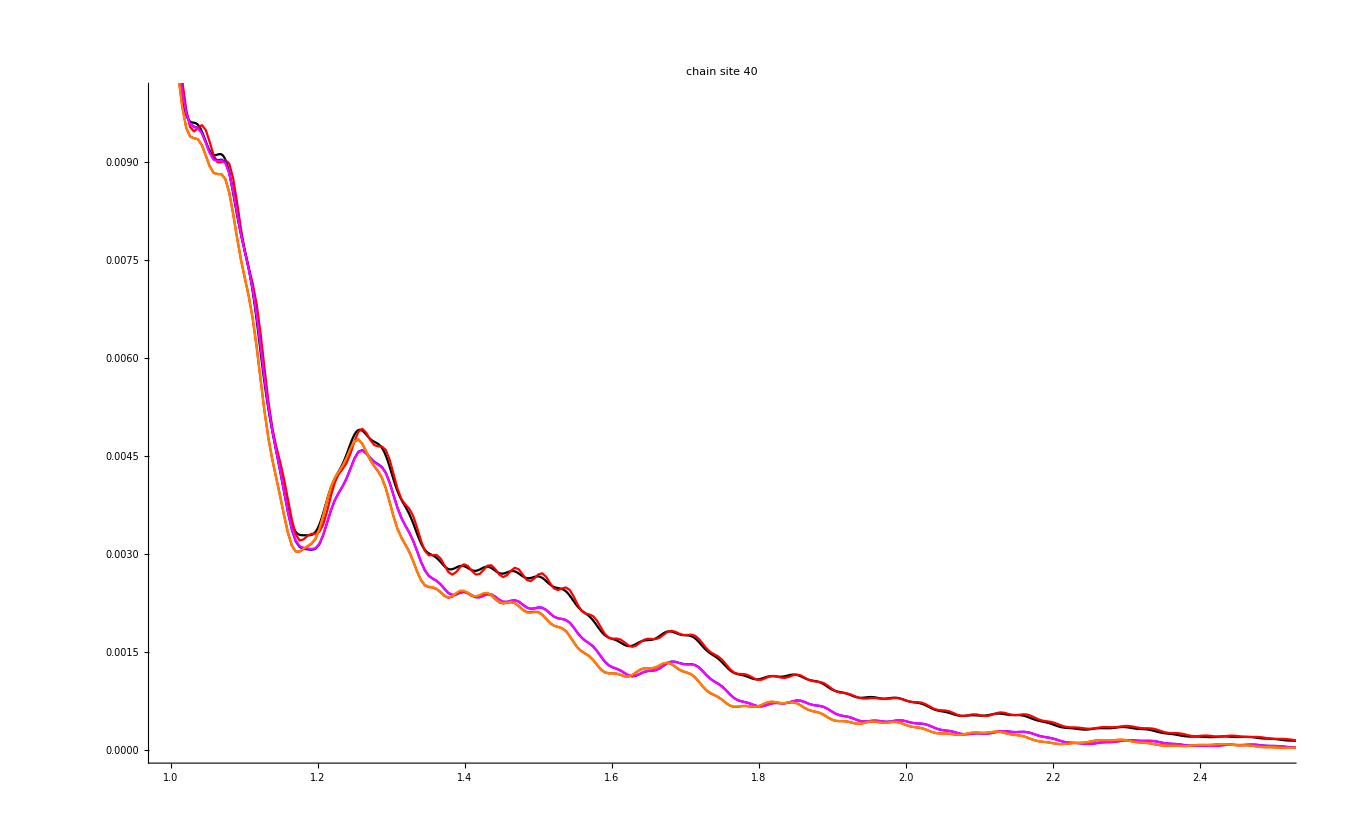

```mathematica
Show[
ListPlot[Transpose[{dataAlex[[All,1]]/0.188365,dataAlexN10[[All,3]]}],PlotRange->{{0,2.5},All},Joined->True,PlotStyle->Black],
ListPlot[Transpose[{dataChi20[[All,1]]*toPs,dataChi20[[All,5]]}],Joined->True,PlotRange->{{0,2.5},All},PlotStyle->Red],
ListPlot[Transpose[{dataMC[[All,1]]*toPs,dataMC[[All,5]]}],Joined->True,PlotRange->{{0,2.5},All},PlotStyle->Blue],

ListPlot[Transpose[{dataTDVP1[[All,1]]*toPs,dataTDVP1[[All,Position[headersTDVP1,"N_41"][[1,1]]]]}],Joined->True,PlotRange->{{0,2.5},All},PlotStyle->Magenta],
ListPlot[Transpose[{toPs*dataTDVP1Q[[All,1]],dataTDVP1Q[[All,Position[headersTDVP1Q,"N_41"][[1,1]]]]}],Joined->True,PlotStyle->Red,PlotRange->All],
ListPlot[Transpose[{toPs*dataTDVP1QP1[[All,1]],dataTDVP1QP1[[All,Position[headersTDVP1QP1,"N_41"][[1,1]]]]}],Joined->True,PlotStyle->Orange,PlotRange->All],
PlotLabel->"chain site 40",
PlotRange->{{1,2.5},{0,0.01}}
]
```

### Population chain site 80

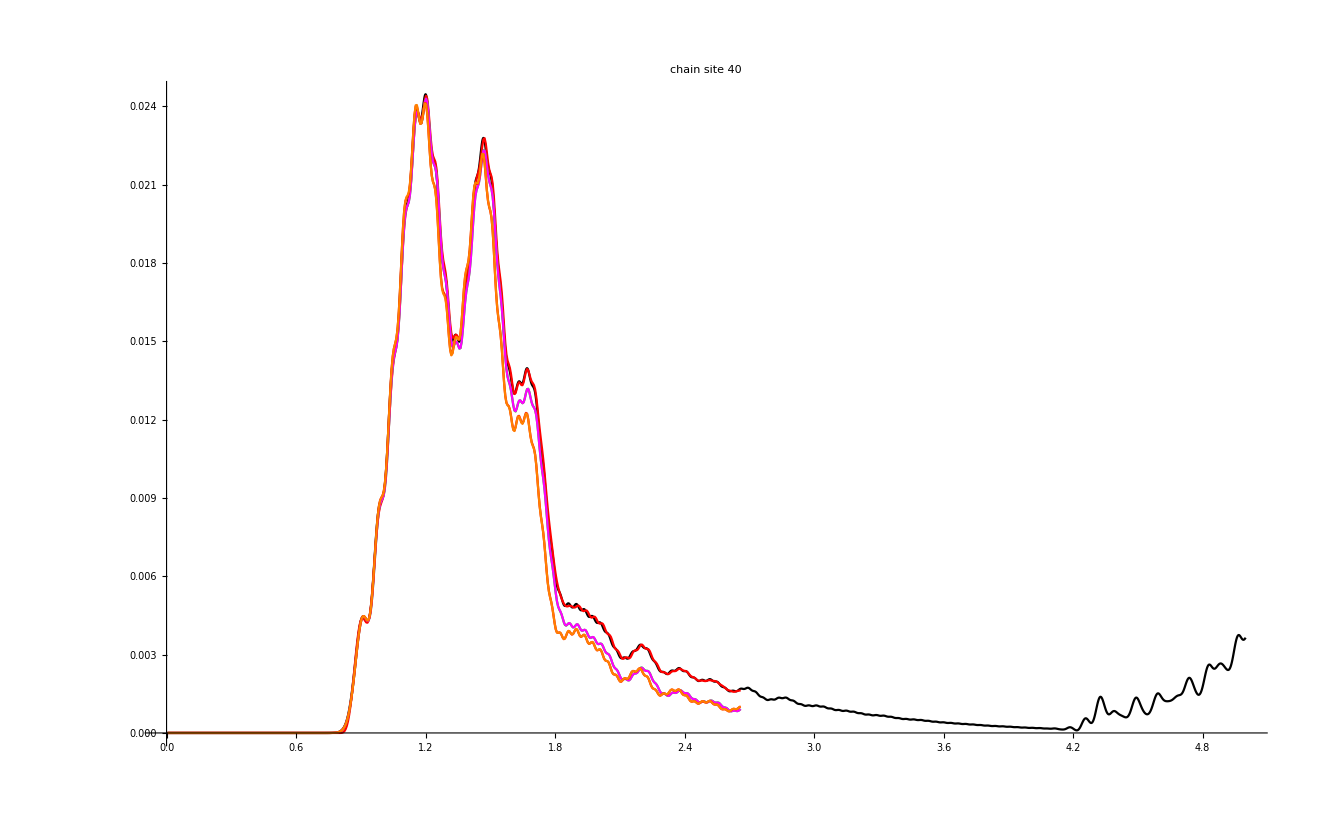

```mathematica
Show[
ListPlot[Transpose[{dataAlex[[All,1]]/0.188365,dataAlexN10[[All,5]]}],PlotRange->{{0,2.5},All},Joined->True,PlotStyle->Black],
ListPlot[Transpose[{dataChi20[[All,1]]*toPs,dataChi20[[All,9]]}],Joined->True,PlotRange->{{0,2.5},All},PlotStyle->Red],

ListPlot[Transpose[{dataMC[[All,1]]*toPs,dataMC[[All,9]]}],Joined->True,PlotRange->{{0,2.5},All},PlotStyle->Green],

ListPlot[Transpose[{dataTDVP1[[All,1]]*toPs,dataTDVP1[[All,Position[headersTDVP1,"N_81"][[1,1]]]]}],Joined->True,PlotRange->{{0,2.5},All},PlotStyle->Magenta],
ListPlot[Transpose[{toPs*dataTDVP1Q[[All,1]],dataTDVP1Q[[All,Position[headersTDVP1Q,"N_81"][[1,1]]]]}],Joined->True,PlotStyle->Red,PlotRange->All],
ListPlot[Transpose[{toPs*dataTDVP1QP1[[All,1]],dataTDVP1QP1[[All,Position[headersTDVP1QP1,"N_81"][[1,1]]]]}],Joined->True,PlotStyle->Orange,PlotRange->All],
PlotRange->All,
PlotLabel->"chain site 40"
]
```

## Closure occupations

```mathematica
headersMC
```

{time,N_11,N_21,N_31,N_41,N_51,N_61,N_71,N_81,N_82,N_83,N_84,N_85,N_86,N_87,Sx_1,Sz_1,re_over,im_over,Norm}

```mathematica
Position[headersMC,"Norm"]
```

{{20}}

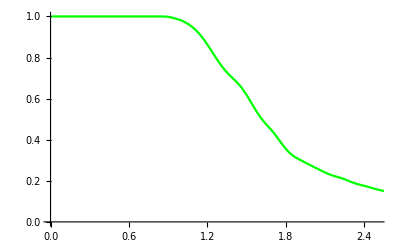

```mathematica
ListPlot[Transpose[{dataMC[[All,1]]*toPs,dataMC[[All,20]]}],Joined->True,PlotRange->{{0,2.5},All},PlotStyle->Green]
```

```mathematica
headersMC
```

{time,N_11,N_12,N_13,N_14,N_15,N_16,N_17,Sx_1,Sz_1,re_over,im_over,Norm}

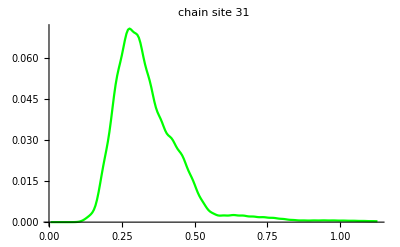

```mathematica
Show[
(*ListPlot[Transpose[{dataAlex[[All,1]]/0.188365,dataAlexN10[[All,2]]}],PlotRange->{{0,2.5},All},Joined->True],*)
(*ListPlot[Transpose[{dataChi20[[All,1]]*toPs,dataChi20[[All,4]]}],Joined->True,PlotRange->{{0,2.5},All},PlotStyle->Red],*)
ListPlot[Transpose[{dataMC[[All,1]]*toPs,dataMC[[All,4]]}],Joined->True,PlotRange->{{0,2.5},All},PlotStyle->Green],
PlotRange->All,
PlotLabel->"chain site 31"
]
```